```mathematica
Attenuation[0.025,0.025,0.1/1000,1.9*10^9,420]
```

b

((0.0791762-0.0211136 ⅈ) BesselJ[1,0.025 √(1583.52 (-Sin[VegetationAtten`Private`alpha-VegetationAtten`Private`phii] Sin[VegetationAtten`Private`thetai]+Sin[VegetationAtten`Private`alpha-VegetationAtten`Private`phis] Sin[VegetationAtten`Private`thetas])^2+(Cos[39.7935 VegetationAtten`Private`beta (Cos[VegetationAtten`Private`alpha-VegetationAtten`Private`phii] Sin[VegetationAtten`Private`thetai]-Cos[VegetationAtten`Private`alpha-VegetationAtten`Private`phis] Sin[VegetationAtten`Private`thetas])]+Sin[39.7935 VegetationAtten`Private`beta (Cos[VegetationAtten`Private`thetai]+Cos[VegetationAtten`Private`thetas])])^2)] (-0.00312567 Cos[ArcCos[(Cos[VegetationAtten`Private`thetai] Sin[VegetationAtten`Private`beta]+Cos[VegetationAtten`Private`beta] Cos[VegetationAtten`Private`alpha-VegetationAtten`Private`phii] Sin[VegetationAtten`Private`thetai])/(√(1-(-Cos[VegetationAtten`Private`beta] Cos[VegetationAtten`Private`thetai]+Cos[VegetationAtten`Private`alpha-VegetationAtten`Private`phii] Sin[VegetationAtten`Private`beta] Sin[VegetationAtten`Private`thetai])^2))]-ArcCos[(-Cos[VegetationAtten`Private`thetas] Sin[VegetationAtten`Private`beta]+Cos[VegetationAtten`Private`beta] Cos[VegetationAtten`Private`alpha-VegetationAtten`Private`phis] Sin[VegetationAtten`Private`thetas])/(√(1-(Cos[VegetationAtten`Private`beta] Cos[VegetationAtten`Private`thetas]+Cos[VegetationAtten`Private`alpha-VegetationAtten`Private`phis] Sin[VegetationAtten`Private`beta] Sin[VegetationAtten`Private`thetas])^2))]] (Cos[VegetationAtten`Private`beta] Cos[VegetationAtten`Private`thetai]-Cos[VegetationAtten`Private`alpha-VegetationAtten`Private`phii] Sin[VegetationAtten`Private`beta] Sin[VegetationAtten`Private`thetai]) (-Cos[VegetationAtten`Private`beta] Cos[VegetationAtten`Private`thetas]-Cos[VegetationAtten`Private`alpha-VegetationAtten`Private`phis] Sin[VegetationAtten`Private`beta] Sin[VegetationAtten`Private`thetas])+0.993749 √(1-(Cos[VegetationAtten`Private`beta] Cos[VegetationAtten`Private`thetai]-Cos[VegetationAtten`Private`alpha-VegetationAtten`Private`phii] Sin[VegetationAtten`Private`beta] Sin[VegetationAtten`Private`thetai])^2) √(1-(-Cos[VegetationAtten`Private`beta] Cos[VegetationAtten`Private`thetas]-Cos[VegetationAtten`Private`alpha-VegetationAtten`Private`phis] Sin[VegetationAtten`Private`beta] Sin[VegetationAtten`Private`thetas])^2)))/(√(1583.52 (-Sin[VegetationAtten`Private`alpha-VegetationAtten`Private`phii] Sin[VegetationAtten`Private`thetai]+Sin[VegetationAtten`Private`alpha-VegetationAtten`Private`phis] Sin[VegetationAtten`Private`thetas])^2+(Cos[39.7935 VegetationAtten`Private`beta (Cos[VegetationAtten`Private`alpha-VegetationAtten`Private`phii] Sin[VegetationAtten`Private`thetai]-Cos[VegetationAtten`Private`alpha-VegetationAtten`Private`phis] Sin[VegetationAtten`Private`thetas])]+Sin[39.7935 VegetationAtten`Private`beta (Cos[VegetationAtten`Private`thetai]+Cos[VegetationAtten`Private`thetas])])^2))

(Cos[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta] ((0.+0. ⅈ)-(3.09324×10^-6-8.24863×10^-7 ⅈ) Cos[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta])-Cos[VegetationAtten`Private`beta] ((0.+0. ⅈ)-(0.000989625-0.0002639 ⅈ) Cos[VegetationAtten`Private`beta] (-0.00312567 Sin[VegetationAtten`Private`alpha]^2 Sin[VegetationAtten`Private`beta]^2+0.993749 (1-Sin[VegetationAtten`Private`alpha]^2 Sin[VegetationAtten`Private`beta]^2))))/(√(Cos[VegetationAtten`Private`beta]^2+Cos[VegetationAtten`Private`alpha]^2 Sin[VegetationAtten`Private`beta]^2)^2)

-0.314391

```mathematica
ClearAll[beta,alpha]
```

{0.0109979,0.0220004,0.0330083,0.0440212,0.0550384,0.0660592,0.0770828,0.0881085,0.0991356,0.110163,0.121191,0.132219,0.143246,0.154273,0.165298,0.176321,0.187344,0.198365,0.209384,0.220402,0.231419,0.242434,0.253448,0.264461,0.275472,0.286483,0.297492,0.3085,0.319508,0.330514,0.34152,0.352525,0.36353,0.374533,0.385537,0.396539,0.407541,0.418543,0.429544,0.440545,0.451545,0.462545,0.473545,0.484544,0.495543,0.506542,0.51754,0.528539,0.539537,0.550535}

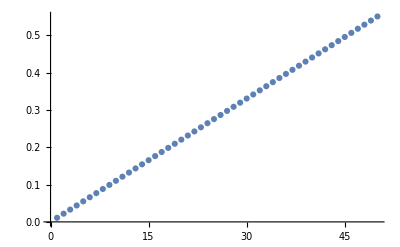

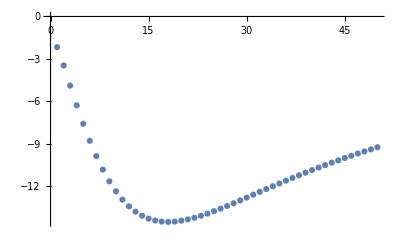

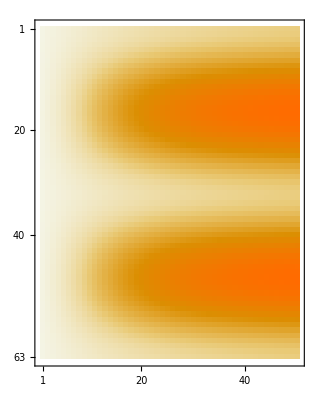

```mathematica
epsilonb=28-I*7;
epsilonl[f_]:=3.1686+(28.938/(1+I*(f/10^9)/18))-I*(0.5672/(f/10^9));
start=1*10^9;
end=30*10^9;
step=1*10^9;
arr=Table[Attenuation[0.114,0.114,1.31,i,epsilonb,Pi/2,Pi/2,0.013],{i,start,end,step}]+Table[Attenuation[0.06,0.06,0.99,i,epsilonb,Pi/2,Pi/2,0.073],{i,start,end,step}]+Table[Attenuation[0.028,0.028,0.82,i,epsilonb,Pi/2,Pi/2,0.041],{i,start,end,step}]+Table[Attenuation[0.007,0.007,0.54,i,epsilonb,Pi/2,Pi/2,5.1],{i,start,end,step}]+Table[Attenuation[0.002,0.002,0.12,i,epsilonb,Pi/2,Pi/2,56],{i,start,end,step}]+Table[Attenuation[0.037,0.037,0.0002,i,epsilonl[i],Pi/2,Pi/2,0.013],{i,start,end,step}]

mat=Table[Attenuation[0.114,0.114,1.31,i,epsilonb,angle,Pi/2,0.013],{angle,0,2*Pi,.1},{i,start,end,step}]+Table[Attenuation[0.06,0.06,0.99,i,epsilonb,angle,Pi/2,0.073],{angle,0,2*Pi,.1},{i,start,end,step}]+Table[Attenuation[0.028,0.028,0.82,i,epsilonb,angle,Pi/2,0.041],{angle,0,2*Pi,.1},{i,start,end,step}]+Table[Attenuation[0.007,0.007,0.54,i,epsilonb,angle,Pi/2,5.1],{angle,0,2*Pi,.1},{i,start,end,step}]+Table[Attenuation[0.002,0.002,0.12,i,epsilonb,angle,Pi/2,56],{angle,0,2*Pi,.1},{i,start,end,step}]+Table[Attenuation[0.037,0.037,0.0002,i,epsilonl[i],angle,Pi/2,420],{angle,0,2*Pi,.1},{i,start,end,step}];
ListPlot[arr]
leafEpsilons=Table[Im[epsilonl[i]],{i,start,end,step}];
ListPlot[leafEpsilons]
MatrixPlot[mat]
```

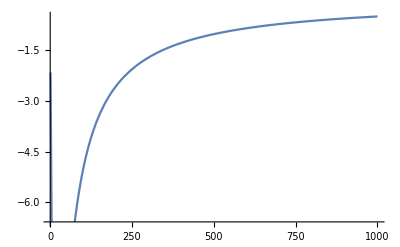

```mathematica
Plot[Im[epsilonl[f]],{f,1,1000}]
```

```mathematica
epsilonl[2*10^9]
```

31.7537-3.45972 ⅈ

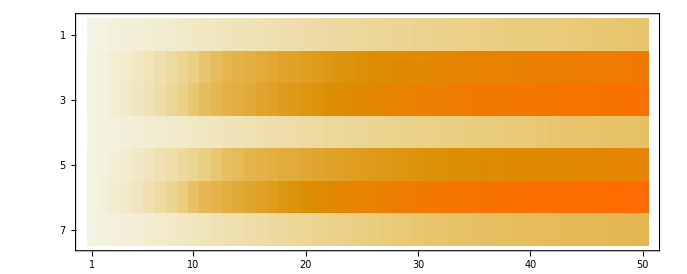

```mathematica
MatrixPlot[mat]
```

```mathematica
Attenuation[0.037,0.037,0.0002,1.9*10^9,epsilonl[1.9*10^9],Pi/2,Pi/2,420]
```

(-Sin[VegetationAtten`Private`beta] Sin[VegetationAtten`Private`alpha-VegetationAtten`Private`phii] ((0.+0. ⅈ)+(0.0000187576-2.02239×10^-6 ⅈ) Sin[VegetationAtten`Private`beta] Sin[VegetationAtten`Private`alpha-VegetationAtten`Private`phii])+(-Cos[VegetationAtten`Private`alpha-VegetationAtten`Private`phii] Cos[VegetationAtten`Private`thetai] Sin[VegetationAtten`Private`beta]-Cos[VegetationAtten`Private`beta] Sin[VegetationAtten`Private`thetai]) ((0.+0. ⅈ)+(0.00444877-0.000479652 ⅈ) (-Cos[VegetationAtten`Private`alpha-VegetationAtten`Private`phii] Cos[VegetationAtten`Private`thetai] Sin[VegetationAtten`Private`beta]-Cos[VegetationAtten`Private`beta] Sin[VegetationAtten`Private`thetai]) (-0.00421636 (Cos[VegetationAtten`Private`beta] Cos[VegetationAtten`Private`thetai]-Cos[VegetationAtten`Private`alpha-VegetationAtten`Private`phii] Sin[VegetationAtten`Private`beta] Sin[VegetationAtten`Private`thetai])^2+0.991567 (1-(Cos[VegetationAtten`Private`beta] Cos[VegetationAtten`Private`thetai]-Cos[VegetationAtten`Private`alpha-VegetationAtten`Private`phii] Sin[VegetationAtten`Private`beta] Sin[VegetationAtten`Private`thetai])^2))))/(√(Sin[VegetationAtten`Private`beta]^2 Sin[VegetationAtten`Private`alpha-VegetationAtten`Private`phii]^2+(-Cos[VegetationAtten`Private`alpha-VegetationAtten`Private`phii] Cos[VegetationAtten`Private`thetai] Sin[VegetationAtten`Private`beta]-Cos[VegetationAtten`Private`beta] Sin[VegetationAtten`Private`thetai])^2)^2)

--

(Cos[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta] ((0.+0. ⅈ)-(0.0000187576-2.02239×10^-6 ⅈ) Cos[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta])-Cos[VegetationAtten`Private`beta] ((0.+0. ⅈ)-(0.00444877-0.000479652 ⅈ) Cos[VegetationAtten`Private`beta] (-0.00421636 Sin[VegetationAtten`Private`alpha]^2 Sin[VegetationAtten`Private`beta]^2+0.991567 (1-Sin[VegetationAtten`Private`alpha]^2 Sin[VegetationAtten`Private`beta]^2))))/(√(Cos[VegetationAtten`Private`beta]^2+Cos[VegetationAtten`Private`alpha]^2 Sin[VegetationAtten`Private`beta]^2)^2)

0.568898

```mathematica
Sin[1]
```

Sin[1]

```mathematica
Table[{i,angle},{i,0,10},{angle,0,Pi,1}]
```

{{{0,0},{0,1},{0,2},{0,3}},{{1,0},{1,1},{1,2},{1,3}},{{2,0},{2,1},{2,2},{2,3}},{{3,0},{3,1},{3,2},{3,3}},{{4,0},{4,1},{4,2},{4,3}},{{5,0},{5,1},{5,2},{5,3}},{{6,0},{6,1},{6,2},{6,3}},{{7,0},{7,1},{7,2},{7,3}},{{8,0},{8,1},{8,2},{8,3}},{{9,0},{9,1},{9,2},{9,3}},{{10,0},{10,1},{10,2},{10,3}}}

```mathematica
Table[Attenuation[0.114,0.114,1.31,1.9*10^9,epsilonb,angle,2*Pi,0.013],{angle,0,Pi,1}]
Sin[Pi/8]
```

--

0

(-Cos[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta] ((0.+0. ⅈ)-(0.00287799-0.000746146 ⅈ) Cos[VegetationAtten`Private`alpha] ((-0.508031+0.00592524 ⅈ) Cos[VegetationAtten`Private`beta]^2-(0.0160619-0.0118505 ⅈ) (1-Cos[VegetationAtten`Private`beta]^2)) Sin[VegetationAtten`Private`beta])-Sin[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta] ((0.+0. ⅈ)+(0.00145769-0.000396118 ⅈ) Sin[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta]))/(√(Cos[VegetationAtten`Private`alpha]^2 Sin[VegetationAtten`Private`beta]^2+Sin[VegetationAtten`Private`alpha]^2 Sin[VegetationAtten`Private`beta]^2)^2)

-0.0000373838+0.0000460901 ⅈ

--

1

(-Sin[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta] ((0.+0. ⅈ)+(0.00145769-0.000396118 ⅈ) Sin[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta])+(-Cos[VegetationAtten`Private`beta] Sin[1]-Cos[1] Cos[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta]) ((0.+0. ⅈ)+(0.00287799-0.000746146 ⅈ) (-Cos[VegetationAtten`Private`beta] Sin[1]-Cos[1] Cos[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta]) ((-0.508031+0.00592524 ⅈ) (Cos[1] Cos[VegetationAtten`Private`beta]-Cos[VegetationAtten`Private`alpha] Sin[1] Sin[VegetationAtten`Private`beta])^2-(0.0160619-0.0118505 ⅈ) (1-(Cos[1] Cos[VegetationAtten`Private`beta]-Cos[VegetationAtten`Private`alpha] Sin[1] Sin[VegetationAtten`Private`beta])^2))))/(√(Sin[VegetationAtten`Private`alpha]^2 Sin[VegetationAtten`Private`beta]^2+(-Cos[VegetationAtten`Private`beta] Sin[1]-Cos[1] Cos[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta])^2)^2)

-0.00104306+0.000293935 ⅈ

--

2

(-Sin[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta] ((0.+0. ⅈ)+(0.00145769-0.000396118 ⅈ) Sin[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta])+(-Cos[VegetationAtten`Private`beta] Sin[2]-Cos[2] Cos[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta]) ((0.+0. ⅈ)+(0.00287799-0.000746146 ⅈ) (-Cos[VegetationAtten`Private`beta] Sin[2]-Cos[2] Cos[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta]) ((-0.508031+0.00592524 ⅈ) (Cos[2] Cos[VegetationAtten`Private`beta]-Cos[VegetationAtten`Private`alpha] Sin[2] Sin[VegetationAtten`Private`beta])^2-(0.0160619-0.0118505 ⅈ) (1-(Cos[2] Cos[VegetationAtten`Private`beta]-Cos[VegetationAtten`Private`alpha] Sin[2] Sin[VegetationAtten`Private`beta])^2))))/(√(Sin[VegetationAtten`Private`alpha]^2 Sin[VegetationAtten`Private`beta]^2+(-Cos[VegetationAtten`Private`beta] Sin[2]-Cos[2] Cos[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta])^2)^2)

-0.00121172+0.000335501 ⅈ

--

3

(-Sin[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta] ((0.+0. ⅈ)+(0.00145769-0.000396118 ⅈ) Sin[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta])+(-Cos[VegetationAtten`Private`beta] Sin[3]-Cos[3] Cos[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta]) ((0.+0. ⅈ)+(0.00287799-0.000746146 ⅈ) (-Cos[VegetationAtten`Private`beta] Sin[3]-Cos[3] Cos[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta]) ((-0.508031+0.00592524 ⅈ) (Cos[3] Cos[VegetationAtten`Private`beta]-Cos[VegetationAtten`Private`alpha] Sin[3] Sin[VegetationAtten`Private`beta])^2-(0.0160619-0.0118505 ⅈ) (1-(Cos[3] Cos[VegetationAtten`Private`beta]-Cos[VegetationAtten`Private`alpha] Sin[3] Sin[VegetationAtten`Private`beta])^2))))/(√(Sin[VegetationAtten`Private`alpha]^2 Sin[VegetationAtten`Private`beta]^2+(-Cos[VegetationAtten`Private`beta] Sin[3]-Cos[3] Cos[VegetationAtten`Private`alpha] Sin[VegetationAtten`Private`beta])^2)^2)

-0.000065669+0.0000530609 ⅈ

{0.0000313042,0.0000313042,0.0000313042,0.0000313042}

Sin[π/8]

```mathematica
$ContextPath
```

{VegetationAtten`,NaturalLanguageLoader`,StreamingLoader`,SymbolicMachineLearningLoader`,NeuralNetworks`,IconizeLoader`,HTTPHandlingLoader`,PacletManager`,System`,Global`}

```mathematica
Attenuation[0.037,0.037,0.0002,1.9*10^9,31-ⅈ*8,0,Pi/4,420]
```

--

0.156086

```mathematica
N[1/7]
```

0.142857

```mathematica
3.7/100
```

0.037

```mathematica
x^2+y^2/.x->1/.y->2
```

5

```mathematica
N[Pi/2]
```

1.5708

```mathematica
epsilonb=28-I*7;
epsilonl[f_]:=3.1686+(28.938/(1+I*(f/10^9)/18))-I*(0.5672/(f/10^9));
start=1*10^9;
end=30*10^9;
step=0.25*10^9;
li=Table[{i,Attenuation[0.114,0.114,1.31,i,epsilonb,0,Pi/2,Pi/4,0.013]+
Attenuation[0.06,0.06,0.99,i,epsilonb,0,Pi/2,Pi/4,0.073]+
Attenuation[0.028,0.028,0.82,i,epsilonb,0,Pi/2,Pi/2,0.041]+
Attenuation[0.007,0.007,0.54,i,epsilonb,0,Pi/2,Pi/2,5.1]+
Attenuation[0.002,0.002,0.12,i,epsilonb,0,Pi/2,Pi/2,56]+
Attenuation[0.037,0.037,0.0002,i,epsilonl[i],0,Pi/2,Pi/2,420]},{i,start,end,step}];
```

```mathematica
Clear[Attenuation]
```

{0.051166+1.01536×10^-10 x+1.45033×10^-19 x^2,1534.37}

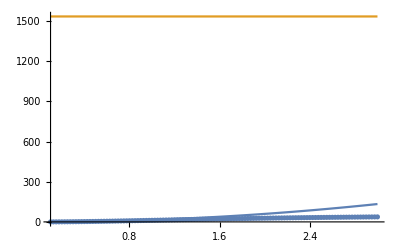

```mathematica
fits=FindFormula[li,x,1,"Error",PerformanceGoal->"Quality"]
Show[Plot[fits,{x,1*10^9,30*10^9},PlotRange->All],ListPlot[li]]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[19.6684+Sin[1. x]^2]

{19.6684+Sin[1. x]^2, | Estimate | Standard Error | t-Statistic | P-Value
a | 19.6684 | 1.13873 | 17.2722 | 2.31753×10^-33
b | 1. | 0. | ∞ | 0.
c | 1. | 9.09891×10^-11 | 1.09903×10^10 | 1.09495941255919×10^-1011
d | 1. | 0. | ∞ | 0.
e | 1. | 0. | ∞ | 0.}

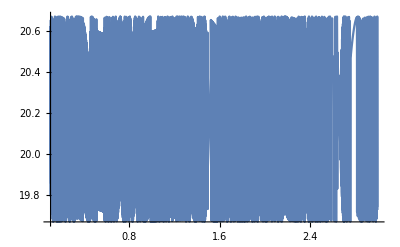

```mathematica
nlm=NonlinearModelFit[li,a+Sin[x/c]^2,{a,b,c,d,e},x]
nlm[{"BestFit","ParameterTable"}]
Show[Plot[nlm[x],{x,1*10^9,30*10^9}],ListPlot[li]]
```

```mathematica
Clear[nlm]
```

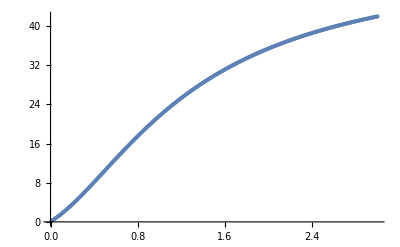

8       10
InterpolatingFunction[{{1. 10 , 3. 10  }}, <>]

```mathematica
epsilonb=28-I*7;
epsilonl[f_]:=3.1686+(28.938/(1+I*(f/10^9)/18))-I*(0.5672/(f/10^9));
start=0.1*10^9;
end=30*10^9;
step=1*10^8;
li=Table[{i,
Attenuation[0.0025,0.0025,0.305,i,epsilonb,0,Pi/2,Pi/2,10]+
Attenuation[0.015,0.015,2.6162,i,epsilonb,0,Pi/2,Pi/4,0.01]+
Attenuation[0.0005,0.0005,0.09,i,epsilonb,0,Pi/2,Pi/2,56]+
Attenuation[0.001,0.001,0.015,i,epsilonl[i],0,Pi/2,Pi/2,420]
}
,{i,start,end,step}];
ListPlot[li]
f=Interpolation[li]
```

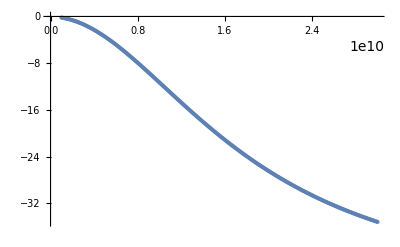

```mathematica
ListPlot[li]
```

```mathematica
Attenuation[0.001,0.001,0.015,1.9*10^9,epsilonl[1.9*10^9],0,Pi/2,Pi/2,420]
```

1.74779

```mathematica
Sqrt[1-(0.001/0.015)^2]
```

0.997775

```mathematica
N[100*(1-10^(3.5/10))]
```

-123.872

```mathematica
f[2*10^9]
```

3.58942

```mathematica
Plot[f[x],{x,1*10^9,30*10^9}]
```

-Graphics-

```mathematica
FourierSeries[Interpolation[li][x],x,1]
```

FourierSeries[                             9       10
InterpolatingFunction[{{1. 10 , 3. 10  }}, <>][x],x,1]

BSplineFunction[{{0., 1.}}, <>]

BSplineFunction[{{0., 1.}}, <>][1000000000]

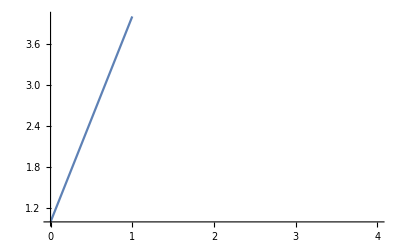

```mathematica
b=BSplineFunction[{1,2,3,4}]
b[1*10^9]
Plot[b[x],{x,0,4}]
```

```mathematica
li
```

{{1000000000,1.65299},{2000000000,3.58942},{3000000000,5.77848},{4000000000,8.11702},{5000000000,10.5181},{6000000000,12.9136},{7000000000,15.2529},{8000000000,17.5015},{9000000000,19.6376},{10000000000,21.649},{11000000000,23.5312},{12000000000,25.2843},{13000000000,26.9122},{14000000000,28.4207},{15000000000,29.817},{16000000000,31.1088},{17000000000,32.3038},{18000000000,33.4097},{19000000000,34.4339},{20000000000,35.3833},{21000000000,36.2642},{22000000000,37.0825},{23000000000,37.8437},{24000000000,38.5526},{25000000000,39.2137},{26000000000,39.8311},{27000000000,40.4084},{28000000000,40.949},{29000000000,41.4558},{30000000000,41.9315}}

```mathematica
GeneralizedLinearModelFit[%130,{x},{x}]
```

FittedModel[5.53309+1.38657×10^-9 x]

```mathematica
Transpose[%128]
```

{{1000000000,2000000000,3000000000,4000000000,5000000000,6000000000,7000000000,8000000000,9000000000,10000000000,11000000000,12000000000,13000000000,14000000000,15000000000,16000000000,17000000000,18000000000,19000000000,20000000000,21000000000,22000000000,23000000000,24000000000,25000000000,26000000000,27000000000,28000000000,29000000000,30000000000},{1.65299,3.58942,5.77848,8.11702,10.5181,12.9136,15.2529,17.5015,19.6376,21.649,23.5312,25.2843,26.9122,28.4207,29.817,31.1088,32.3038,33.4097,34.4339,35.3833,36.2642,37.0825,37.8437,38.5526,39.2137,39.8311,40.4084,40.949,41.4558,41.9315}}

```mathematica
str=OpenWrite[]
Write[str,li]
Close[str]
```

OutputStream[…]

/var/folders/j5/zjbd__c92h76zqc6n0yw0msw0000gn/T/m000001447271

```mathematica
FilePrint[%]
```

{{1000000000, 1.6529919189203408}, {1100000000, 1.8320901705793144}, 
 {1200000000, 2.01472305779518}, {1300000000, 2.200777631713725}, 
 {1400000000, 2.3901401884509186}, {1500000000, 2.5826967343836795}, 
 {1600000000, 2.7783333179830554}, {1700000000, 2.9769362808822346}, 
 {1800000000, 3.17839245753961}, {1900000000, 3.382589340538248}, 
 {2000000000, 3.589415221772561}, {2100000000, 3.7987593158880406}, 
 {2200000000, 4.0105118700440885}, {2300000000, 4.224564262674641}, 
 {2400000000, 4.440809093051772}, {2500000000, 4.659140262904179}, 
 {2600000000, 4.8794530509833995}, {2700000000, 5.101644181234092}, 
 {2800000000, 5.32561188506661}, {2900000000, 5.551255958123003}, 
 {3000000000, 5.778477811854882}, {3100000000, 6.007180520181011}, 
 {3200000000, 6.237268861457795}, {3300000000, 6.468649355971572}, 
 {3400000000, 6.701230299144359}, {3500000000, 6.934921790632912}, 
 {3600000000, 7.169635759492038}, {3700000000, 7.4052859855670174}, 
 {3800000000, 7.64178811727511}, {3900000000, 7.879059685932792}, 
 {4000000000, 8.11702011678183}, {4100000000, 8.355590736865521}, 
 {4200000000, 8.594694779903202}, {4300000000, 8.834257388309624}, 
 {4400000000, 9.074205612502988}, {4500000000, 9.314468407643265}, 
 {4600000000, 9.55497662794007}, {4700000000, 9.795663018666557}, 
 {4800000000, 10.03646220601312}, {4900000000, 10.277310684911896}, 
 {5000000000, 10.51814680495995}, {5100000000, 10.758910754565763}, 
 {5200000000, 10.999544543440495}, {5300000000, 11.239991983552011}, 
 {5400000000, 11.480198668656074}, {5500000000, 11.720111952515671}, 
 {5600000000, 11.959680925915615}, {5700000000, 12.19885639257586}, 
 {5800000000, 12.437590844063394}, {5900000000, 12.675838433798344}, 
 {6000000000, 12.913554950246798}, {6100000000, 13.150697789388309}, 
 {6200000000, 13.387225926542792}, {6300000000, 13.623099887637622}, 
 {6400000000, 13.858281719991767}, {6500000000, 14.092734962690612}, 
 {6600000000, 14.32642461662085}, {6700000000, 14.559317114232005}, 
 {6800000000, 14.79138028908689}, {6900000000, 15.02258334526034}, 
 {7000000000, 15.25289682664239}, {7100000000, 15.48229258619797}, 
 {7200000000, 15.710743755233173}, {7300000000, 15.938224712713987}, 
 {7400000000, 16.164711054681266}, {7500000000, 16.390179563802107}, 
 {7600000000, 16.614608179095647}, {7700000000, 16.837975965868065}, 
 {7800000000, 17.060263085889403}, {7900000000, 17.281450767842056}, 
 {8000000000, 17.501521278068477}, {8100000000, 17.72045789164345}, 
 {8200000000, 17.938244863793887}, {8300000000, 18.154867401687305}, 
 {8400000000, 18.370311636607813}, {8500000000, 18.584564596536786}, 
 {8600000000, 18.797614179153463}, {8700000000, 19.009449125269125}, 
 {8800000000, 19.220058992706697}, {8900000000, 19.42943413063619}, 
 {9000000000, 19.637565654375035}, {9100000000, 19.844445420660687}, 
 {9200000000, 20.050066003402012}, {9300000000, 20.254420669914275}, 
 {9400000000, 20.45750335764187}, {9500000000, 20.65930865137144}, 
 {9600000000, 20.859831760937368}, {9700000000, 21.059068499420523}, 
 {9800000000, 21.257015261840106}, {9900000000, 21.45366900433829}, 
 {10000000000, 21.649027223855413}, {10100000000, 21.843087938294136}, 
 {10200000000, 22.0358496671694}, {10300000000, 22.22731141274071}, 
 {10400000000, 22.417472641622734}, {10500000000, 22.606333266869793}, 
 {10600000000, 22.793893630529187}, {10700000000, 22.980154486658062}, 
 {10800000000, 23.165116984797873}, {10900000000, 23.34878265390056}, 
 {11000000000, 23.531153386699955}, {11100000000, 23.712231424521722}, 
 {11200000000, 23.89201934252491}, {11300000000, 24.07052003536817}, 
 {11400000000, 24.247736703293064}, {11500000000, 24.423672838617357}, 
 {11600000000, 24.59833221263028}, {11700000000, 24.771718862882654}, 
 {11800000000, 24.94383708086347}, {11900000000, 25.11469140005561}, 
 {12000000000, 25.28428658436254}, {12100000000, 25.45262761689814}, 
 {12200000000, 25.619719689131607}, {12300000000, 25.785568190379994}, 
 {12400000000, 25.950178697639643}, {12500000000, 26.113556965749442}, 
 {12600000000, 26.27570891787752}, {12700000000, 26.436640636323876}, 
 {12800000000, 26.596358353630908}, {12900000000, 26.754868443994614}, 
 {13000000000, 26.912177414968465}, {13100000000, 27.06829189945235}, 
 {13200000000, 27.223218647959943}, {13300000000, 27.376964521155976}, 
 {13400000000, 27.529536482657363}, {13500000000, 27.680941592090115}, 
 {13600000000, 27.831186998395747}, {13700000000, 27.980279933379812}, 
 {13800000000, 28.128227705495835}, {13900000000, 28.275037693858447}, 
 {14000000000, 28.420717342478397}, {14100000000, 28.56527415471363}, 
 {14200000000, 28.708715687930304}, {14300000000, 28.851049548366454}, 
 {14400000000, 28.992283386193858}, {14500000000, 29.132424890770974}, 
 {14600000000, 29.271481786081452}, {14700000000, 29.409461826353184}, 
 {14800000000, 29.54637279185141}, {14900000000, 29.68222248484111}, 
 {15000000000, 29.81701872571345}, {15100000000, 29.950769349270487}, 
 {15200000000, 30.083482201164014}, {15300000000, 30.21516513448297}, 
 {15400000000, 30.345826006484803}, {15500000000, 30.475472675466346}, 
 {15600000000, 30.60411299776945}, {15700000000, 30.73175482491706}, 
 {15800000000, 30.8584060008753}, {15900000000, 30.984074359437518}, 
 {16000000000, 31.10876772172633}, {16100000000, 31.232493893809337}, 
 {16200000000, 31.355260664425053}, {16300000000, 31.477075802814998}, 
 {16400000000, 31.597947056658597}, {16500000000, 31.717882150106934}, 
 {16600000000, 31.83688878191259}, {16700000000, 31.954974623651424}, 
 {16800000000, 32.072147318033736}, {16900000000, 32.18841447730133}, 
 {17000000000, 32.30378368170739}, {17100000000, 32.41826247807644}, 
 {17200000000, 32.531858378441356}, {17300000000, 32.64457885875469}, 
 {17400000000, 32.75643135767148}, {17500000000, 32.867423275401244}, 
 {17600000000, 32.97756197262623}, {17700000000, 33.08685476948386}, 
 {17800000000, 33.19530894461053}, {17900000000, 33.302931734244844}, 
 {18000000000, 33.409730331388104}, {18100000000, 33.515711885019435}, 
 {18200000000, 33.62088349936362}, {18300000000, 33.72525223321016}, 
 {18400000000, 33.82882509928089}, {18500000000, 33.9316090636444}, 
 {18600000000, 34.033611045175746}, {18700000000, 34.1348379150595}, 
 {18800000000, 34.23529649633427}, {18900000000, 34.33499356347714}, 
 {19000000000, 34.433935842026614}, {19100000000, 34.53213000824216}, 
 {19200000000, 34.629582688799196}, {19300000000, 34.726300460517606}, 
 {19400000000, 34.82228985012331}, {19500000000, 34.91755733404004}, 
 {19600000000, 35.0121093382117}, {19700000000, 35.10595223795272}, 
 {19800000000, 35.19909235782589}, {19900000000, 35.29153597154647}, 
 {20000000000, 35.3832893019108}, {20100000000, 35.47435852074935}, 
 {20200000000, 35.564749748902294}, {20300000000, 35.65446905621688}, 
 {20400000000, 35.74352246156583}, {20500000000, 35.83191593288534}, 
 {20600000000, 35.91965538723225}, {20700000000, 36.00674669085921}, 
 {20800000000, 36.09319565930713}, {20900000000, 36.17900805751399}, 
 {21000000000, 36.26418959993918}, {21100000000, 36.34874595070291}, 
 {21200000000, 36.4326827237395}, {21300000000, 36.51600548296427}, 
 {21400000000, 36.59871974245317}, {21500000000, 36.68083096663415}, 
 {21600000000, 36.76234457049056}, {21700000000, 36.843265919774815}, 
 {21800000000, 36.923600331232706}, {21900000000, 37.003353072837186}, 
 {22000000000, 37.082529364031444}, {22100000000, 37.16113437598043}, 
 {22200000000, 37.23917323183068}, {22300000000, 37.31665100697777}, 
 {22400000000, 37.39357272934079}, {22500000000, 37.46994337964377}, 
 {22600000000, 37.5457678917032}, {22700000000, 37.621051152721705}, 
 {22800000000, 37.695798003586965}, {22900000000, 37.77001323917573}, 
 {23000000000, 37.843701608663096}, {23100000000, 37.91686781583548}, 
 {23200000000, 37.989516519408106}, {23300000000, 38.061652333346274}, 
 {23400000000, 38.133279827189675}, {23500000000, 38.204403526380446}, 
 {23600000000, 38.27502791259337}, {23700000000, 38.34515742406942}, 
 {23800000000, 38.41479645595094}, {23900000000, 38.483949360619526}, 
 {24000000000, 38.55262044803516}, {24100000000, 38.62081398607737}, 
 {24200000000, 38.68853420088772}, {24300000000, 38.75578527721317}, 
 {24400000000, 38.822571358750864}, {24500000000, 38.88889654849343}, 
 {24600000000, 38.95476490907487}, {24700000000, 39.02018046311697}, 
 {24800000000, 39.08514719357602}, {24900000000, 39.149669044089535}, 
 {25000000000, 39.21374991932285}, {25100000000, 39.2773936853158}, 
 {25200000000, 39.340604169828715}, {25300000000, 39.40338516268822}, 
 {25400000000, 39.4657404161323}, {25500000000, 39.527673645154664}, 
 {25600000000, 39.589188527848464}, {25700000000, 39.65028870574865}, 
 {25800000000, 39.71097778417382}, {25900000000, 39.77125933256655}, 
 {26000000000, 39.83113688483261}, {26100000000, 39.89061393967897}, 
 {26200000000, 39.949693960950206}, {26300000000, 40.00838037796361}, 
 {26400000000, 40.06667658584269}, {26500000000, 40.12458594584892}, 
 {26600000000, 40.18211178571205}, {26700000000, 40.23925739995851}, 
 {26800000000, 40.296026050237906}, {26900000000, 40.35242096564795}, 
 {27000000000, 40.408445343057195}, {27100000000, 40.46410234742585}, 
 {27200000000, 40.519395112124855}, {27300000000, 40.57432673925249}, 
 {27400000000, 40.628900299949116}, {27500000000, 40.683118834709894}, 
 {27600000000, 40.7369853536951}, {27700000000, 40.790502837038396}, 
 {27800000000, 40.843674235152804}, {27900000000, 40.89650246903459}, 
 {28000000000, 40.94899043056455}, {28100000000, 41.0011409828073}, 
 {28200000000, 41.0529569603083}, {28300000000, 41.10444116938804}, 
 {28400000000, 41.15559638843458}, {28500000000, 41.20642536819304}, 
 {28600000000, 41.25693083205331}, {28700000000, 41.30711547633499}, 
 {28800000000, 41.3569819705698}, {28900000000, 41.40653295778223}, 
 {29000000000, 41.455771054767084}, {29100000000, 41.50469885236483}, 
 {29200000000, 41.55331891573472}, {29300000000, 41.601633784625285}, 
 {29400000000, 41.64964597364233}, {29500000000, 41.69735797251473}, 
 {29600000000, 41.74477224635753}, {29700000000, 41.79189123593299}, 
 {29800000000, 41.838717357908685}, {29900000000, 41.88525300511365}, 
 {30000000000, 41.93150054679192}}

```mathematica
DeleteFile[str]
```

DeleteFile::strs: String or non-empty list of strings is expected at position 1 in DeleteFile[OutputStream[/var/folders/j5/zjbd__c92h76zqc6n0yw0msw0000gn/T/m000001447271,3]].

DeleteFile[OutputStream[/var/folders/j5/zjbd__c92h76zqc6n0yw0msw0000gn/T/m000001447271,3]]

```mathematica
epsilonb=28-I*7;
epsilonl[f_]:=3.1686+(28.938/(1+I*(f/10^9)/18))-I*(0.5672/(f/10^9));
start=0.1*10^9;
end=30*10^9;
step=1*10^7;
pine=Table[{i,
Attenuation[0.0025,0.0025,0.305,i,epsilonb,0,Pi/2,Pi/2,10]+
Attenuation[0.015,0.015,2.6162,i,epsilonb,0,Pi/2,Pi/4,0.01]+
Attenuation[0.0005,0.0005,0.09,i,epsilonb,0,Pi/2,Pi/2,56]+
Attenuation[0.001,0.001,0.015,i,epsilonl[i],0,Pi/2,Pi/2,420]},{i,start,end,step}];
oak=Table[{i,
Attenuation[0.114,0.114,1.31,i,epsilonb,0,Pi/2,Pi/4,0.013]+
Attenuation[0.06,0.06,0.99,i,epsilonb,0,Pi/2,Pi/4,0.073]+
Attenuation[0.028,0.028,0.82,i,epsilonb,0,Pi/2,Pi/2,0.041]+
Attenuation[0.007,0.007,0.54,i,epsilonb,0,Pi/2,Pi/2,5.1]+
Attenuation[0.002,0.002,0.12,i,epsilonb,0,Pi/2,Pi/2,56]+
Attenuation[0.037,0.037,0.0002,i,epsilonl[i],0,Pi/2,Pi/2,420]},{i,start,end,step}];
Export["pine.txt",pine,"CSV"];
Export["oak.txt",oak,"CSV"];
```

```mathematica
Export["test.txt",pine,"CSV"]
```

test.txt

```mathematica
FindFile["test.txt"]
```

/Users/michaeldeleo/test.txt